## Documentation

### Atlas Raw Data Structures

JSON / JLink -Xmx : http://reference.wolfram.com/mathematica/ref/message/Import/nojmem.html

atlas documentation : https://atlas.ripe.net/docs/data_struct 
RFC4950 ICMP Extensions for Multiprotocol Label Switching : http://tools.ietf.org/html/rfc4950
paris traceroute version : http://www.paris-traceroute.net

howto/AddErrorBarsToChartsAndPlots

## Data Source

```mathematica
ClearAll[fetchJSON];
Needs["JLink`"];
fetchJSON[resultNumber_Integer, friendlyName_String]:=Module[
{defaultCacheDir, fullPathToCache,uri, jsonData},
defaultCacheDir=FileNameJoin[{NotebookDirectory[], "data"}];
fullPathToCache=FileNameJoin[{defaultCacheDir,"RIPE-Atlas-measurement-traceroute-"<>ToString[resultNumber]<>"-"<>friendlyName<>".json"}];
uri="https://atlas.ripe.net/api/v1/measurement/"<>ToString[resultNumber]<>"/result";

(* PREPARE JSON PARSER FOR LARGE FILES  *)
InstallJava[];
ReinstallJava[CommandLine->"java",JVMArguments->"-Xmx2024m"];

If[FileExistsQ[fullPathToCache],
jsonData=Import[fullPathToCache,"JSON"],
Module[{},
jsonData=Import[uri,"JSON"];
Export[fullPathToCache,jsonData,"JSON"]];
(* CLEAN UP JSON PARSER *)
UninstallJava[];
(* --->RETURNING *)
jsonData
]
];
```

#### Read JSON file

```mathematica
ClearAll[tData];
```

```mathematica
(* 80mb JSON file *)
If[False,tData=fetchJSON[1608005, "digifortress"],False];
(* 20mb JSON file *)
If[True,tData=fetchJSON[1664934,"pacificEndpoint-Oahu"],False];
(* Special case with x->* values *)
If[False,tData={{"af"->4,"dst_addr"->"72.129.45.3","dst_name"->"72.129.45.3","endtime"->1399737713,"from"->"24.94.68.214","fw"->4610,"group_id"->1664934,"msm_id"->1664934,"msm_name"->"Traceroute","paris_id"->14,"prb_id"->1178,"proto"->"ICMP","result"->{{"hop"->1,"result"->{{"x"->"*"},{"x"->"*"},{"x"->"*"}}},{"hop"->2,"result"->{{"from"->"24.25.230.137","rtt"->282.411,"size"->28,"ttl"->254},{"from"->"24.25.230.137","rtt"->251.608,"size"->28,"ttl"->254},{"from"->"24.25.230.137","rtt"->514.685,"size"->28,"ttl"->254}}},{"hop"->3,"result"->{{"from"->"72.129.45.68","rtt"->586.958,"size"->68,"ttl"->253},{"from"->"72.129.45.68","rtt"->71.773,"size"->68,"ttl"->253},{"from"->"72.129.45.68","rtt"->20.124,"size"->68,"ttl"->253}}}},"size"->40,"src_addr"->"192.168.5.228","timestamp"->1399737697,"type"->"traceroute"}},False];
```

```mathematica
Dimensions[tData]
```

{26718,17}

## Transcoding

```mathematica
Clear[walkAtlasTraceroute];
walkAtlasTraceroute[traceroute_]:=Message["walkAtlasTraceroute forward declaration here; waiting for body to be implemented"];
```

### Map Atlas JSON Traceroute To Summary

#### Utility Functions

```mathematica
(* HST is -10 from GMT -- *)
unixTimeToHST[x_Integer]:=DateList[AbsoluteTime[{1970,1,1,2,0,0}]+x,TimeZone->-10];
(* TEST *)
unixTimeToHST[1399725833]
```

{2014,5,10,9,43,53.}

```mathematica
(* General implementation *)
ClearAll[ipToString];
ipToString::usage="to avoid confusion of non-routable IPv4 in use at multiple probe locations, add a suffix of _probeID to the string representation";
ipToString[prbID_,ipV4_String]:=ipToString[prbID,ipV4]="_"<>ipV4<>"_"<>ToString[prbID];


ClearAll[uniquifyNonRoutable];
uniquifyNonRoutable::usage="Ensure common non routable IPv4 addresses are suffixed with their probe name";
(* MESSAGES *)
uniquifyNonRoutable::unexpectedArg="probeID->`1`, IPv4->`2`";
(* IMPLEMENTATION *)
uniquifyNonRoutable[prbID_Integer,ipV4_String/; StringMatchQ[ipV4,"192.168."~~___]]:=ipToString[prbID,ipV4];
uniquifyNonRoutable[prbID_Integer ,ipV4_String/; StringMatchQ[ipV4,"10."~~___]]:=ipToString[prbID,ipV4];
uniquifyNonRoutable[prbID_Integer ,ipV4_String/; StringMatchQ[ipV4,"172."~~Alternatives @@ToString /@Range[16,31]~~"."~~___]]:=ipToString[prbID,ipV4];
(* The following is the general case where anything else should be the IPv4 address *)
uniquifyNonRoutable[prbID_ ,ipV4_String]:=uniquifyNonRoutable[prbID,ipV4]=ipV4;

(* SPECIAL CASE for ASTRIX routed values *)
uniquifyNonRoutable[prbID_Integer,aSymbol_Symbol]:=ToString[prbID]<>ToString[aSymbol];

(* NOTIFY ON UNKNOWN ARGUMENT *) 
(* uniquifyNonRoutable[probeID_,ipV4_]:=Message[uniquifyNonRoutable::unexpectedArg,"probeID->`1` IPv4->`2`"];*)

(* TEST *)
uniquifyNonRoutable["pxxxx", #]&/@{"192.168.100.1","10.100.100.1","172.16.0.1", "172.31.255.255","172.32.1.1"}//TableForm
```

192.168.100.1
10.100.100.1
172.16.0.1
172.31.255.255
172.32.1.1

```mathematica
uniquifyNonRoutable["pxxxx", #]&/@{a,b}//TableForm
```

uniquifyNonRoutable[pxxxx,a]
uniquifyNonRoutable[pxxxx,b]

```mathematica
(* sHopInterval : normalizes a single ping in the hop's interval test *)
ClearAll[sHopInterval];
sHopInterval::usage="sHopInterval flattens out results of individual ICMP results from a single hop interval - including optional results - into a standard format. This implies some of that optional info might well be dropped.  See normalizedResult::canonicalResult";
normalizedResult::canonicalResult="{from, rtt, size, ttl, errorsIfAny}";
(* MESSAGES *)
sHopInterval::icmpnext="(opt) icmpnext chunk omitted";
sHopInterval::unexpectedArg="`1`";
(* IMPLEMENTATION *) 

(* GOOD RESULTS - return as good values *)
sHopInterval[{"from"->from_, "rtt" ->rtt_,"size"->size_Integer, "ttl"->ttl_Integer}]:= {"from"->from, "rtt" ->rtt,"size"->size, "ttl"->ttl};
(* icmpext (optional)  *)
sHopInterval[{"from"->from_, "icmpext"->icmpext_List,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= 
Block[{},
{"from"->from, "rtt" ->rtt,"size"->size, "ttl"->ttl,"icmpext"->icmpext}];

(* BAD RESULTS -- return as packet drop *)
sHopInterval[{"x"->"*"}]=
{"PACKET_DROP"->{"x"->"*"}};

sHopInterval[{"error"->"sendto failed: Network is unreachable"}] := {"PACKET_DROP"->{"error"->"sendto failed: Network is unreachable"}};

sHopInterval[{"err"->err_,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= {"rtt" ->rtt,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"err"->err}};

sHopInterval[{"err"->err_,"from"->from_,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"rtt" ->rtt,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"err"->err}};

sHopInterval[{"err"->err_,"from"->from_,"ittl"->ittl_,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"rtt" ->rtt,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"err"->err, "ittl"->ittl}};

(* ittl (optional) TimeToLive in packet that triggered the error ICMP. Omitted if equal to 1 (int) *)
sHopInterval[{"from"->from_, "ittl"->ittl_Integer,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= {"from"->from, "rtt" ->rtt,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"ittl"->ittl}};

(* late (optional) means the timeout exceed the wait time.  *)
sHopInterval[{"from"->from_, "ittl"->ittl_Integer,"late" ->late_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"ittl"->ittl,"late" ->late}};

sHopInterval[{"from"->from_, "late" ->late_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"late" ->late}};

sHopInterval[{"from"->from_, "icmpext"->icmpext_List,"ittl"->ittl_Integer,"rtt" ->rtt_,"size"->size_, "ttl"->ttl_}]:= 
{"from"->from, "rtt" ->rtt,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"ittl"->ittl,"icmpext"->icmpext}};

sHopInterval[{"from"->from_, "icmpext"->icmpext_List,"ittl"->ittl_Integer,"late" ->late_,"size"->size_, "ttl"->ttl_}]:= 
{"from"->from, "size"->size, "ttl"->ttl,"PACKET_DROP"->{"ittl"->ittl,"icmpext"->icmpext, "late"->late}};

sHopInterval[{"from"->from_, "icmpext"->icmpext_,"late" ->late_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"icmpext"->icmpext,"late" ->late}};

sHopInterval[{"from"->from_, "icmpext"->icmpext_,"ittl" ->ittl_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"icmpext"->icmpext,"ittl" ->ittl}};

sHopInterval[{"edst"->edst_String,"from"->from_, "ittl"->ittl_Integer,"late" ->late_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"edst"->edst,"ittl"->ittl,"late" ->late}};

sHopInterval[{"edst"->edst_String,"from"->from_, "rtt"->rtt_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"edst"->edst,"rtt"->rtt}};

sHopInterval[{"edst"->edst_String,"from"->from_, "late" ->late_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"edst"->edst,"late" ->late}};

sHopInterval[{"edst"->edst_String,"from"->from_, "icmpext"->icmpext_,"late" ->late_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"edst"->edst,"icmpext"->icmpext,"late" ->late}};


sHopInterval[{"edst"->edst_String,"from"->from_, "icmpext" ->icmpext_,"rtt"->rtt_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"edst"->edst,"icmpext" ->icmpext,"rtt"->rtt}};

sHopInterval[{"dup"->dup_,"edst"->edst_String,"from"->from_, "icmpext" ->icmpext_,"rtt"->rtt_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"dup"->dup,"edst"->edst,"icmpext" ->icmpext,"rtt"->rtt}};

sHopInterval[{"dup"->dup_,"edst"->edst_String,"from"->from_, "ittl" ->ittl_,"rtt"->rtt_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"dup"->dup,"edst"->edst,"ittl" ->ittl,"rtt"->rtt}};

sHopInterval[{"dup"->dup_,"from"->from_, "rtt"->rtt_,"size"->size_, "ttl"->ttl_}]:= {"from"->from,"size"->size, "ttl"->ttl,"PACKET_DROP"->{"dup"->dup,"rtt"->rtt}};

(* NOTIFY ON UNKNOWN ARGUMENT *) 
sHopInterval [x_]:= Message[sHopInterval::unexpectedArg,x];
(* TEST *)
walkAtlasTraceroute[tData[[3;;4]]]//TableForm
```

Message::name: Message name "walkAtlasTraceroute forward declaration here; waiting for body to be implemented" is not of the form symbol::name or symbol::name::language.

Message[walkAtlasTraceroute forward declaration here; waiting for body to be implemented]

```mathematica
ClearAll[sHopTestsAllErrors];
sHopTestsAllErrors[prbID_Integer,hopID_Integer,errs_List]:=Block[{candidateFrom,fromValToUse,astrix},
candidateFrom=DeleteCases[DeleteDuplicates["from"/.errs],"from"];

astrix=If[False,
Unique["p"<>ToString[prbID]<>"H"<>ToString[hopID]<>"z"],"p"<>ToString[prbID]<>"_"<>ToString[hopID]<>"_"<>ToString[RandomInteger[{1,100}]]];

fromValToUse=If[candidateFrom≠{},candidateFrom[[1]],astrix];
(* --->RETURNING *)
{"from" -> uniquifyNonRoutable[prbID,fromValToUse],"droppedPacketCount"->Length[errs]}
]

ClearAll[sHopTestsSummary];
sHopTestsSummary[prbID_Integer,hopID_Integer,allResults_List,successPositions_List,errsPosition_List]:=
      Block[{candidateFrom,fromVal, sizeVal, ttlVal, errorFreeRTTs, errorCount,successSlice},
successSlice=allResults[[successPositions]];

(* Assert : successful RTTs must have a property "from"*)
candidateFrom=DeleteDuplicates["from"/.successSlice];
       (* assert : from, size and ttl are all the same *)
       fromVal = uniquifyNonRoutable[prbID,candidateFrom[[1]]];
       
 errorFreeRTTs = "rtt"/.successSlice;
       (* process erroredResults *)
       errorCount = If[errsPosition=={},0,Length[errsPosition]];
(* --->RETURNING *)
       {
"from" -> fromVal,
"rtt"->errorFreeRTTs,
"droppedPacketCount"->errorCount
}
];
```

```mathematica
(* sHopTests : summarizes RTTs and errors from a specific hop in the traceroute for a probe *)
ClearAll[sHopTests];
(* MESSAGES *)
sHopTests::unexpectedArg = "`1`";
(* IMPLEMENTATION *)
sHopTests["prb_id" -> prbID_, {"hop" -> hopID_, "result" -> testsInsideHop_List}] := 
  Block[{allResults,rttDrops,rttSuccess},
     allResults = sHopInterval /@ testsInsideHop;
     (* Exected form returned is 
     {from,rtt,size,ttl,{"icmpext"->icmpext}}
     or
     {from,rtt,size,ttl,{}}
     or
     {from,rtt, size, ttl,{"PACKET_DROP"}}
     or
     {"UNKNOWN",-1, -1, -1,{"PACKET_DROP"}}
     *)

     (* Divide by timeouts versus results *)
rttDrops=Flatten[Position[allResults,"PACKET_DROP"->_][[All,1]]];
rttSuccess=Complement[Range[1,Length[allResults]],rttDrops];

     (* classifiy all non-timeout results *)
     If[Length[rttSuccess] ==0,
sHopTestsAllErrors[prbID,hopID,allResults], sHopTestsSummary[prbID,hopID,allResults,rttSuccess,rttDrops ]]];
(* NOTIFY ON UNKNOWN ARGUMENT *) 
sHopTests[x_] := Message[sHopTests::unexpectedArg, x];
(* TEST *)
walkAtlasTraceroute[tData[[8;;9]]] // TableForm
```

Message[walkAtlasTraceroute forward declaration here; waiting for body to be implemented]

```mathematica
(* walkProbeTraceroute : summarizes an individual probe's traceroute *)
ClearAll[walkProbeTraceroute];
(* MESSAGES *)
walkProbeTraceroute::usage="walkProbeTraceroute works through the results";
walkProbeTraceroute::unexpectedArg="`1`";
(* IMPLEMENTATION *)
(* Assert : hop is dropped in the expectation walkProbeTraceroute is always called in traversal order of the list of hops *)
walkProbeTraceroute[prbID_Rule,hopsInTraceroute_List]:= 
sHopTests[prbID,#]&/@ hopsInTraceroute;
(* NOTIFY ON UNKNOWN ARGUMENT *) 
walkProbeTraceroute[x_]:=Message[walkProbeTraceroute::unexpectedArg,x];
(* TEST *)
walkAtlasTraceroute[tData[[8;;9]]]//TableForm
```

Message[walkAtlasTraceroute forward declaration here; waiting for body to be implemented]

```mathematica
(* walkAtlasTraceroute : Initiates the walk of traceroute results *)
ClearAll[walkAtlasTraceroute];
walkAtlasTraceroute::usage="Summarizes results from all probes";

walkAtlasTraceroute[{af_Rule,dstAddr_Rule,dstName_Rule, endTime_Rule,from_Rule, "fw"->fw_,groupID_Rule,msmID_Rule,msmName_Rule,parisID_Rule,prbID_Rule,proto_Rule,"result"->result_List,size_Rule,srcAddr_Rule,timeStamp_Rule,type_Rule}] :=Block[
{},
(* ---> RETURNING *)
{
prbID,
proto,
parisID,
type,
"fw"->fw,
"start"->unixTimeToHST["timestamp"/.timeStamp], 
proto,
"hopAndRTTs"->walkProbeTraceroute[prbID,result]
}
];

(* Generalize for a list *)
walkAtlasTraceroute[aList_List]:= walkAtlasTraceroute /@ aList;
walkAtlasTraceroute[aList_List, probes_List]:= Block[
{
aListMatching
},

aListMatching=Cases[aList,{__,"prb_id"->prbID_,__}/;MemberQ[probes,prbID]];
(* Remove all data other than the selectd probes *)
walkAtlasTraceroute /@ aListMatching
] ;
(* TEST *)
walkAtlasTraceroute[tData[[1;;9]],{10546}]//TableForm
```

prb_id→10546 | proto→ICMP | paris_id→1 | type→traceroute | fw→4610 | start→{2014,3,30,20,1,15.} | proto→ICMP | hopAndRTTs→{{from→_192.168.1.1_10546,rtt→{0.768,0.589,0.552},droppedPacketCount→0},{from→70.95.176.1,droppedPacketCount→3},{from→24.25.230.229,rtt→{13.539,12.337,12.268},droppedPacketCount→0},{from→72.129.46.164,droppedPacketCount→3},{from→72.129.45.45,droppedPacketCount→3},{from→72.129.45.67,rtt→{17.769,18.431,18.791},droppedPacketCount→0},{from→24.25.225.149,droppedPacketCount→3},{from→206.197.210.18,rtt→{20.204,22.225,21.757},droppedPacketCount→0},{from→66.192.254.82,rtt→{22.326,22.191,21.189},droppedPacketCount→0},{from→66.162.247.242,rtt→{22.019,21.26,21.499},droppedPacketCount→0},{from→205.172.1.1,rtt→{21.975,22.003,21.505},droppedPacketCount→0}}
prb_id→10546 | proto→ICMP | paris_id→2 | type→traceroute | fw→4610 | start→{2014,3,30,20,16,22.} | proto→ICMP | hopAndRTTs→{{from→_192.168.1.1_10546,rtt→{0.694,0.583,0.551},droppedPacketCount→0},{from→70.95.176.1,droppedPacketCount→3},{from→24.25.230.229,rtt→{14.342,43.656,11.608},droppedPacketCount→0},{from→72.129.46.164,droppedPacketCount→3},{from→72.129.45.45,droppedPacketCount→3},{from→72.129.45.67,rtt→{18.009,18.854,18.655},droppedPacketCount→0},{from→24.25.225.149,droppedPacketCount→3},{from→206.197.210.18,rtt→{20.853,20.725,19.419},droppedPacketCount→0},{from→66.192.254.82,rtt→{22.381,21.523,20.676},droppedPacketCount→0},{from→66.162.247.242,rtt→{19.639,21.859,21.699},droppedPacketCount→0},{from→205.172.1.1,rtt→{20.158,19.885,17.447},droppedPacketCount→0}}

```mathematica
(* pathsOnly extracts the unique traceroute path from all tests *)
ClearAll[pathOnly];
pathOnly::usage="Given a JSON traceroute list, distill down to the unique set of traceroute paths";
pathOnly::unexpectedArg="`1`";
(* IMPLEMENTATION *)
pathOnly[{"prb_id"->prbID_Integer,"proto"->proto_String,"paris_id"->parisID_Integer,"type"->type_String,"fw"->fw_Integer,"start"->start_List, "proto"->proto_String, "hopAndRTTs"->hopsAndRTTs_List}]:= 
Block[
{path,pathWithProbeStart,valToReturn},
path=Prepend["from"/. hopsAndRTTs, ToString[prbID]];
valToReturn=Rule@@#&/@Partition[path,2,1]; 
(* --->RETURNING *)
DeleteDuplicates[Sort[valToReturn,OrderedQ[{First[#1],First[#2]}&]]]
];
pathOnly[aList_List]:=pathOnly/@ aList;
(* NOTIFY ON UNKNOWN ARGUMENT *) 
pathOnly[x_]:=Message[pathOnly::unexpectedArg,x];
(* TEST *)
Block[{traces, paths},
traces=tData[[1;;2]];
traces=tData[[1;;1000]];
paths=pathOnly[walkAtlasTraceroute[traces]];

Dimensions[paths]]
```

{1000}

## Visualizations

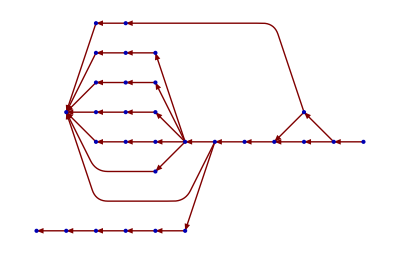
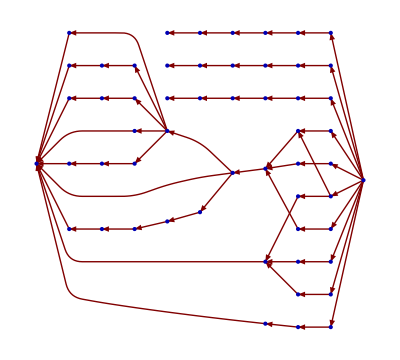
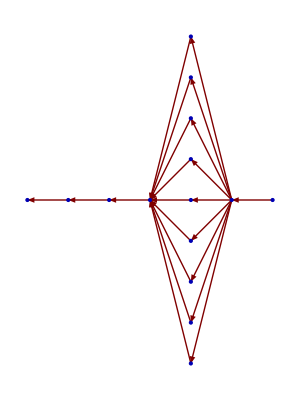
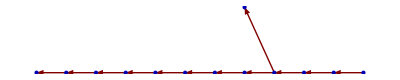
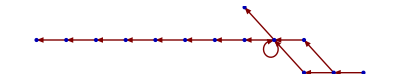
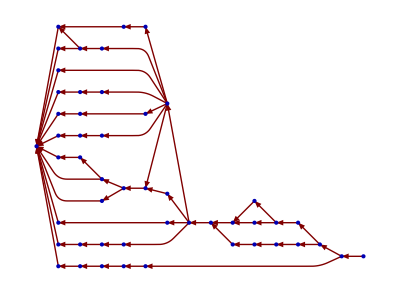
1165 | -Graphics-
1178 | -Graphics-
15111 | -Graphics-
2289 | -Graphics-
12735 | -Graphics-
10546 | -Graphics-
14720 | -Graphics-

```mathematica
Table[Block[
{},{probeVal,LayeredGraphPlot[
Flatten[pathOnly[walkAtlasTraceroute[tData[[1;;]],{probeVal}]],1],
Right,
MultiedgeStyle->True, 
DirectedEdges->True, 
VertexLabeling->Automatic]}],{probeVal, {1165,1178,15111,2289,12735,10546,14720}}]//TableForm
```

### Scratch

#### Extracting values from nested rules in JSON data

http://mathematica.stackexchange.com/questions/3111/extracting-values-from-nested-rules-in-json-data

```mathematica
LayeredGraphPlot[
Flatten[pathOnly[walkAtlasTraceroute[tData[[1;;]]]],1],
Right,
MultiedgeStyle->True, 
DirectedEdges->True, 
VertexLabeling->Automatic]
```

-Graphics-